```mathematica
MatrixForm[quantcheckiter]
```

(1.06447×10^-10 | 2.82668×10^6 | 3.3507596542511816556×10^6 | {T→20000} | 1.06447×10^-10 | 20000 | {T→20000} | 2.82668×10^6 | {T→3.35076×10^6} | (6340.94 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.48542×10^7)/((1/1000000+1.68638×10^-10 T) T^4 BesselK[2,1/(1/1000000+1.68638×10^-10 T)])
1.06447×10^-10 | 1.41334×10^6 | 3.3507596542511816556×10^6 | {T→3.3507596542511816556×10^6} | 1.06447×10^-10 | 3.3507596542511816556×10^6 | {T→3.3507596542511816556×10^6} | 1.41334×10^6 | {T→3.35076×10^6} | (6340.98 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (2.56842×10^10)/((1/1000000+1.68638×10^-10 T) T^4 BesselK[2,1/(1/1000000+1.68638×10^-10 T)])
1.06447×10^-10 | 1.41327×10^6 | 3.3507596542511816556×10^6 | {T→3.3507596542511816556×10^6} | 1.06447×10^-10 | 3.35076×10^6 | {T→3.35076×10^6} | 1.41327×10^6 | {T→3.35076×10^6} | (6340.98 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (2.56816×10^10)/((1/1000000+1.68638×10^-10 T) T^4 BesselK[2,1/(1/1000000+1.68638×10^-10 T)])
1.06447×10^-10 | 1.41334×10^6 | 3.3507596542511816556×10^6 | {T→3.3507596542511816556×10^6} | 1.06447×10^-10 | 3.3507596542511816556×10^6 | {T→3.3507596542511816556×10^6} | 1.41334×10^6 | {T→3.35076×10^6} | (6340.98 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (2.56842×10^10)/((1/1000000+1.68638×10^-10 T) T^4 BesselK[2,1/(1/1000000+1.68638×10^-10 T)])
1.06447×10^-10 | 1.41327×10^6 | 3.3507596542511816556×10^6 | {T→3.35076×10^6} | 1.06447×10^-10 | 3.35076×10^6 | {T→3.35076×10^6} | 1.41327×10^6 | {T→3.35076×10^6} | (6340.98 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (2.56816×10^10)/((1/1000000+1.68638×10^-10 T) T^4 BesselK[2,1/(1/1000000+1.68638×10^-10 T)]))

```mathematica
Q0synch//.solsT
```

1.72757×10^8

```mathematica
resultclasslocal//.solsT
```

3.49928827018996×10^-775

```mathematica
jclass0raw
```

0.0015847

```mathematica
ne*fgamfullfreeforint*NIntegrate[grandit,{th,0,Pi},{gammareal,1/Sin[th],Infinity}]//.solsT
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

5.82966471242612×10^6

```mathematica
jgeo
```

1/2

```mathematica
solsT
```

{T→3.3507596542511816556×10^6}

```mathematica
resultclasslocal=resultclass//.{Thetax->Thetadep};
jclassthermalnew=ne*fgamfullfree*resultclasslocal*jclass0raw//.solsT
```

1.72757×10^8

```mathematica
FullSimplify[Q0synch]
```

((304758.+51.3937 T) BesselK[3,1/(1.×10^-6+1.68638×10^-10 T)])/BesselK[2,1/(1.×10^-6+1.68638×10^-10 T)]

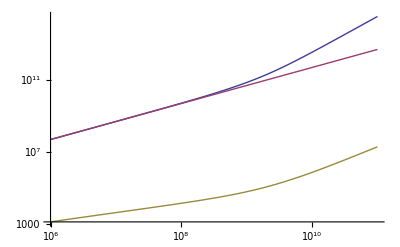

```mathematica
LogLogPlot[{Q0synch,(304757.55338578625+51.39374490531404 T),Q0ff},{T,10^6,10^11}]
```

```mathematica
Nscalayers
```

1

```mathematica
Hsca
```

1.09139×10^11

```mathematica
Q0synch
```

(3.04758×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]

```mathematica
ne
```

3.20521×10^13

```mathematica
npairs
```

4.80989223120593×10^-743

```mathematica
Series[Q0synch,{T,0,10}]
```

304758.315280241+51.394 T+O[T]^11

```mathematica
fun=gammax*(gammax-1)//.{gammax->1/Sqrt[1-T]}
Series[fun,{T,0,10}]
```

(-1+1/(√(1-T)))/(√(1-T))

T/2+(5 T^2)/8+(11 T^3)/16+(93 T^4)/128+(193 T^5)/256+(793 T^6)/1024+(1619 T^7)/2048+(26333 T^8)/32768+(53381 T^9)/65536+(215955 T^10)/262144+O[T]^11

```mathematica
T^4/T^(7/2)
```

√T

```mathematica
tauradabs//.solsT
tauradsca//.solsT
```

1.07267×10^-11

1.50176

```mathematica
npairs
nb
me*c^2/kb
```

7.24084×10^17

6.41041×10^13

5.92986×10^9

```mathematica
solsT[[1]]
uapairs0//.solsT[[1]]
ubpairs0//.solsT[[1]]
ucpairs0//.solsT[[1]]
udpairs0//.solsT[[1]]
Upairs0//.solsT[[1]]
Upairs//.solsT[[1]]
npairs//.solsT[[1]]
```

T→1.2212317453187870986×10^9

2.29254×10^20

2.6271×10^21

1.42216286103117×10^-4330

2.31878224036595×10^-4329

2.85635×10^21

1.22088×10^11

7.24084×10^17

```mathematica
nrad
npairs
```

3.54014×10^18

7.24084×10^17

```mathematica
uapairs0/(kb*T)//.solsT[[1]]
```

1.35967×10^27

```mathematica
e1//.solsT[[1]]
e2//.solsT[[1]]
```

0.00778438

1.1354838653×10^-4343

```mathematica
sigmat
sigmakn
sigmaes
```

6.65077×10^-25

(6.65077×10^-25)/(1+4.49702×10^-10 T)

(6.65077×10^-25)/((1+730.453/T^2) (1+4.49702×10^-10 T))

```mathematica
solsT={T->10^9,npairs->10^(10)}
```

{T→1000000000,1.93691×10^11→10000000000}

```mathematica
solsT[[2,2]]
```

10000000000

```mathematica
(* npairs netotforomegape gammae Hsca Habs solsT solsTrad Tc Tout Trad myie myu4vel myb Q0ff Q0synch tauradsca tauradabs *)
MatrixForm[itercheckiter]
```

(5.14843×10^16 | 3.74538×10^18 | 1.25296 | 1.40286×10^11 | 1.40286×10^11 | {T→500000000} | {T→500000000} | 500000000 | 500000000 | 500000000 | 2.66752×10^12 | 0.01 | 2.82668×10^6 | (2.87654 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.09515×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 4.88304 | 6.22039×10^-10
4.37825×10^19 | 7.06937×10^24 | 1.12648 | 1.71396×10^11 | 1.3774×10^14 | {T→250000000} | {T→250000000} | 250000000 | 250000000 | 250000000 | 2.85419×10^19 | 0.01 | 2.82668×10^6 | (2311.69 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (4.89829×10^14 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 5278.94 | 0.0035591
1.59999×10^9 | 4.53357×10^19 | 1.06324 | 1.71434×10^11 | 1.17088×10^17 | {T→125000000} | {T→125000000} | 125000000 | 125000000 | 125000000 | 1.84715×10^18 | 0.01 | 2.82668×10^6 | (1.96465×10^6 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (4.16293×10^17 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 4.72628×10^6 | 19548.7
1.93691×10^11 | 3.20521×10^13 | 1.03162 | 1.09142×10^11 | 5.45735×10^10 | {T→250000000} | {T→250000000} | 250000000 | 250000000 | 250000000 | 1.26274×10^11 | 0.01 | 2.82668×10^6 | (1.43834 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04773×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 2.09155 | 8.77396×10^-10
5.17447×10^15 | 3.22499×10^13 | 1.06324 | 1.09513×10^11 | 5.50873×10^10 | {T→500000000} | {T→500000000} | 500000000 | 500000000 | 500000000 | 2.68113×10^11 | 0.01 | 2.82668×10^6 | (1.44696 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.06599×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 1.91746 | 1.22868×10^-10
1.27934×10^18 | 3.27398×10^22 | 1.12648 | 1.71051×10^11 | 1.38927×10^13 | {T→250000000} | {T→250000000} | 250000000 | 250000000 | 250000000 | 8.34005×10^17 | 0.01 | 2.82668×10^6 | (233.632 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (4.95047×10^13 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 532.445 | 0.0000362803
1.59999×10^9 | 4.53356×10^19 | 1.06324 | 1.71433×10^11 | 3.42141×10^15 | {T→125000000} | {T→125000000} | 125000000 | 125000000 | 125000000 | 1.84715×10^18 | 0.01 | 2.82668×10^6 | (57409.1 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (1.21645×10^16 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 138106. | 16.6919
1.93691×10^11 | 3.20521×10^13 | 1.03162 | 1.09142×10^11 | 5.45735×10^10 | {T→250000000} | {T→250000000} | 250000000 | 250000000 | 250000000 | 1.26274×10^11 | 0.01 | 2.82668×10^6 | (1.43834 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04773×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 2.09155 | 8.77396×10^-10
5.17447×10^15 | 3.22499×10^13 | 1.06324 | 1.09513×10^11 | 5.50873×10^10 | {T→500000000} | {T→500000000} | 500000000 | 500000000 | 500000000 | 2.68113×10^11 | 0.01 | 2.82668×10^6 | (1.44696 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.06599×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 1.91746 | 1.22868×10^-10
1.27934×10^18 | 3.27398×10^22 | 1.12648 | 1.71051×10^11 | 1.38927×10^13 | {T→250000000} | {T→250000000} | 250000000 | 250000000 | 250000000 | 8.34005×10^17 | 0.01 | 2.82668×10^6 | (233.632 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (4.95047×10^13 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 532.445 | 0.0000362803
1.59999×10^9 | 4.53356×10^19 | 1.06324 | 1.71433×10^11 | 3.42141×10^15 | {T→125000000} | {T→125000000} | 125000000 | 125000000 | 125000000 | 1.84715×10^18 | 0.01 | 2.82668×10^6 | (57409.1 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (1.21645×10^16 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 138106. | 16.6919
1.93691×10^11 | 3.20521×10^13 | 1.03162 | 1.09142×10^11 | 5.45735×10^10 | {T→250000000} | {T→250000000} | 250000000 | 250000000 | 250000000 | 1.26274×10^11 | 0.01 | 2.82668×10^6 | (1.43834 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04773×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 2.09155 | 8.77396×10^-10
5.17447×10^15 | 3.22499×10^13 | 1.06324 | 1.09513×10^11 | 5.50873×10^10 | {T→500000000} | {T→500000000} | 500000000 | 500000000 | 500000000 | 2.68113×10^11 | 0.01 | 2.82668×10^6 | (1.44696 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.06599×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 1.91746 | 1.22868×10^-10
1.27934×10^18 | 3.27398×10^22 | 1.12648 | 1.71051×10^11 | 1.38927×10^13 | {T→250000000} | {T→250000000} | 250000000 | 250000000 | 250000000 | 8.34005×10^17 | 0.01 | 2.82668×10^6 | (233.632 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (4.95047×10^13 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 532.445 | 0.0000362803
1.59999×10^9 | 4.53356×10^19 | 1.06324 | 1.71433×10^11 | 3.42141×10^15 | {T→125000000} | {T→125000000} | 125000000 | 125000000 | 125000000 | 1.84715×10^18 | 0.01 | 2.82668×10^6 | (57409.1 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (1.21645×10^16 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 138106. | 16.6919
1.93691×10^11 | 3.20521×10^13 | 1.03162 | 1.09142×10^11 | 5.45735×10^10 | {T→250000000} | {T→250000000} | 250000000 | 250000000 | 250000000 | 1.26274×10^11 | 0.01 | 2.82668×10^6 | (1.43834 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04773×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 2.09155 | 8.77396×10^-10
5.17447×10^15 | 3.22499×10^13 | 1.06324 | 1.09513×10^11 | 5.50873×10^10 | {T→500000000} | {T→500000000} | 500000000 | 500000000 | 500000000 | 2.68113×10^11 | 0.01 | 2.82668×10^6 | (1.44696 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.06599×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 1.91746 | 1.22868×10^-10
1.27934×10^18 | 3.27398×10^22 | 1.12648 | 1.71051×10^11 | 1.38927×10^13 | {T→250000000} | {T→250000000} | 250000000 | 250000000 | 250000000 | 8.34005×10^17 | 0.01 | 2.82668×10^6 | (233.632 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (4.95047×10^13 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 532.445 | 0.0000362803
1.59999×10^9 | 4.53356×10^19 | 1.06324 | 1.71433×10^11 | 3.42141×10^15 | {T→125000000} | {T→125000000} | 125000000 | 125000000 | 125000000 | 1.84715×10^18 | 0.01 | 2.82668×10^6 | (57409.1 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (1.21645×10^16 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 138106. | 16.6919
1.93691×10^11 | 3.20521×10^13 | 1.03162 | 1.09142×10^11 | 5.45735×10^10 | {T→250000000} | {T→250000000} | 250000000 | 250000000 | 250000000 | 1.26274×10^11 | 0.01 | 2.82668×10^6 | (1.43834 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04773×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)] | 2.09155 | 8.77396×10^-10)

```mathematica
(* npairs netotforomegape gammae Hsca Habs solsT solsTrad Tc Tout Trad myie myu4vel myb Q0ff Q0synch tauradsca tauradabs *)
MatrixForm[itercheckiter]
```

(7.83501×10^8 | 3.74538×10^18 | 1.25296 | 1.40286×10^11 | 1.40286×10^11 | {T→1.833864693369679831×10^8} | {T→1.833864693369679831×10^8} | 1.833864693369679831×10^8 | 1.833864693369679831×10^8 | 1.833864693369679831×10^8 | 9.53748×10^11 | 0.01 | 2.82668×10^6 | (2.87654 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.09515×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24052×10^17 | 3.20521×10^13 | 1.04639 | 1.0914×10^11 | 5.45714×10^10 | {T→1.2211745400527510515×10^9} | {T→1.2211745400527510515×10^9} | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 8.4144×10^11 | 0.01 | 2.82668×10^6 | (1.4383 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04765×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
2.8010509771757×10^-740 | 3.20521×10^13 | 1.3089 | 1.71432×10^11 | 1.93639×10^15 | {T→3.3507596542572752208×10^6} | {T→3.3507596542572752208×10^6} | 3.3507596542572752208×10^6 | 3.3507596542572752208×10^6 | 3.3507596542572752208×10^6 | 9.53753×10^11 | 0.01 | 2.82668×10^6 | (32491.7 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.88474×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24084×10^17 | 3.20521×10^13 | 1.00085 | 1.09139×10^11 | 5.45693×10^10 | {T→1.2212317453187870986×10^9} | {T→1.2212317453187870986×10^9} | 1.2212317453187870986×10^9 | 1.2212317453187870986×10^9 | 1.2212317453187870986×10^9 | 8.41431×10^11 | 0.01 | 2.82668×10^6 | (1.43827 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04758×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
2.80105097717506×10^-740 | 3.20521×10^13 | 1.30892 | 1.71432×10^11 | 1.93648×10^15 | {T→3.3507596542572741989×10^6} | {T→3.3507596542572741989×10^6} | 3.3507596542572741989×10^6 | 3.3507596542572741989×10^6 | 3.3507596542572741989×10^6 | 9.53753×10^11 | 0.01 | 2.82668×10^6 | (32493.2 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.88504×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24084×10^17 | 3.20521×10^13 | 1.00085 | 1.09139×10^11 | 5.45693×10^10 | {T→1.2212317453187870986×10^9} | {T→1.2212317453187870986×10^9} | 1.2212317453187870986×10^9 | 1.2212317453187870986×10^9 | 1.2212317453187870986×10^9 | 8.41431×10^11 | 0.01 | 2.82668×10^6 | (1.43827 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04758×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
2.80105097717506×10^-740 | 3.20521×10^13 | 1.30892 | 1.71432×10^11 | 1.93648×10^15 | {T→3.3507596542572741989×10^6} | {T→3.3507596542572741989×10^6} | 3.3507596542572741989×10^6 | 3.3507596542572741989×10^6 | 3.3507596542572741989×10^6 | 9.53753×10^11 | 0.01 | 2.82668×10^6 | (32493.2 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.88504×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24084×10^17 | 3.20521×10^13 | 1.00085 | 1.09139×10^11 | 5.45693×10^10 | {T→1.2212317453187870986×10^9} | {T→1.2212317453187870986×10^9} | 1.2212317453187870986×10^9 | 1.2212317453187870986×10^9 | 1.2212317453187870986×10^9 | 8.41431×10^11 | 0.01 | 2.82668×10^6 | (1.43827 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04758×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
2.80105097717506×10^-740 | 3.20521×10^13 | 1.30892 | 1.71432×10^11 | 1.93648×10^15 | {T→3.3507596542572741989×10^6} | {T→3.3507596542572741989×10^6} | 3.3507596542572741989×10^6 | 3.3507596542572741989×10^6 | 3.3507596542572741989×10^6 | 9.53753×10^11 | 0.01 | 2.82668×10^6 | (32493.2 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.88504×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24084×10^17 | 3.20521×10^13 | 1.00085 | 1.09139×10^11 | 5.45693×10^10 | {T→1.2212317453187870986×10^9} | {T→1.2212317453187870986×10^9} | 1.2212317453187870986×10^9 | 1.2212317453187870986×10^9 | 1.2212317453187870986×10^9 | 8.41431×10^11 | 0.01 | 2.82668×10^6 | (1.43827 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04758×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
2.80105097717506×10^-740 | 3.20521×10^13 | 1.30892 | 1.71432×10^11 | 1.93648×10^15 | {T→3.3507596542572741989×10^6} | {T→3.3507596542572741989×10^6} | 3.3507596542572741989×10^6 | 3.3507596542572741989×10^6 | 3.3507596542572741989×10^6 | 9.53753×10^11 | 0.01 | 2.82668×10^6 | (32493.2 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.88504×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24084×10^17 | 3.20521×10^13 | 1.00085 | 1.09139×10^11 | 5.45693×10^10 | {T→1.2212317453187870986×10^9} | {T→1.2212317453187870986×10^9} | 1.2212317453187870986×10^9 | 1.2212317453187870986×10^9 | 1.2212317453187870986×10^9 | 8.41431×10^11 | 0.01 | 2.82668×10^6 | (1.43827 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04758×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
2.80105097717506×10^-740 | 3.20521×10^13 | 1.30892 | 1.71432×10^11 | 1.93648×10^15 | {T→3.3507596542572741989×10^6} | {T→3.3507596542572741989×10^6} | 3.3507596542572741989×10^6 | 3.3507596542572741989×10^6 | 3.3507596542572741989×10^6 | 9.53753×10^11 | 0.01 | 2.82668×10^6 | (32493.2 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.88504×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24084×10^17 | 3.20521×10^13 | 1.00085 | 1.09139×10^11 | 5.45693×10^10 | {T→1.2212317453187870986×10^9} | {T→1.2212317453187870986×10^9} | 1.2212317453187870986×10^9 | 1.2212317453187870986×10^9 | 1.2212317453187870986×10^9 | 8.41431×10^11 | 0.01 | 2.82668×10^6 | (1.43827 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04758×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
2.80105097717506×10^-740 | 3.20521×10^13 | 1.30892 | 1.71432×10^11 | 1.93648×10^15 | {T→3.3507596542572741989×10^6} | {T→3.3507596542572741989×10^6} | 3.3507596542572741989×10^6 | 3.3507596542572741989×10^6 | 3.3507596542572741989×10^6 | 9.53753×10^11 | 0.01 | 2.82668×10^6 | (32493.2 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.88504×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24084×10^17 | 3.20521×10^13 | 1.00085 | 1.09139×10^11 | 5.45693×10^10 | {T→1.2212317453187870986×10^9} | {T→1.2212317453187870986×10^9} | 1.2212317453187870986×10^9 | 1.2212317453187870986×10^9 | 1.2212317453187870986×10^9 | 8.41431×10^11 | 0.01 | 2.82668×10^6 | (1.43827 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04758×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
2.80105097717506×10^-740 | 3.20521×10^13 | 1.30892 | 1.71432×10^11 | 1.93648×10^15 | {T→3.3507596542572741989×10^6} | {T→3.3507596542572741989×10^6} | 3.3507596542572741989×10^6 | 3.3507596542572741989×10^6 | 3.3507596542572741989×10^6 | 9.53753×10^11 | 0.01 | 2.82668×10^6 | (32493.2 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.88504×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24084×10^17 | 3.20521×10^13 | 1.00085 | 1.09139×10^11 | 5.45693×10^10 | {T→1.2212317453187870986×10^9} | {T→1.2212317453187870986×10^9} | 1.2212317453187870986×10^9 | 1.2212317453187870986×10^9 | 1.2212317453187870986×10^9 | 8.41431×10^11 | 0.01 | 2.82668×10^6 | (1.43827 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04758×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
2.80105097717506×10^-740 | 3.20521×10^13 | 1.30892 | 1.71432×10^11 | 1.93648×10^15 | {T→3.3507596542572741989×10^6} | {T→3.3507596542572741989×10^6} | 3.3507596542572741989×10^6 | 3.3507596542572741989×10^6 | 3.3507596542572741989×10^6 | 9.53753×10^11 | 0.01 | 2.82668×10^6 | (32493.2 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.88504×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24084×10^17 | 3.20521×10^13 | 1.00085 | 1.09139×10^11 | 5.45693×10^10 | {T→1.2212317453187870986×10^9} | {T→1.2212317453187870986×10^9} | 1.2212317453187870986×10^9 | 1.2212317453187870986×10^9 | 1.2212317453187870986×10^9 | 8.41431×10^11 | 0.01 | 2.82668×10^6 | (1.43827 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04758×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)])

```mathematica
MatrixForm[itercheckiter]
```

(7.83501×10^8 | 3.74538×10^18 | 1.25296 | 1.40286×10^11 | 1.40286×10^11 | {T→1.833864693369679831×10^8} | {T→1.833864693369679831×10^8} | 1.833864693369679831×10^8 | 1.833864693369679831×10^8 | 1.833864693369679831×10^8 | 9.53748×10^11 | 0.01 | 2.82668×10^6 | (2.87654 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.09515×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24052×10^17 | 3.20521×10^13 | 1.04639 | 1.0914×10^11 | 5.45714×10^10 | {T→1.2211745400527510515×10^9} | {T→1.2211745400527510515×10^9} | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 8.4144×10^11 | 0.01 | 2.82668×10^6 | (1.4383 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04765×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
5.16095×10^8 | 3.20521×10^13 | 1.3089 | 1.71432×10^11 | 1.93639×10^15 | {T→1.2211745400527510515×10^8} | {T→1.2211745400527510515×10^8} | 1.2211745400527510515×10^8 | 1.2211745400527510515×10^8 | 1.2211745400527510515×10^8 | 1.68257×10^18 | 0.01 | 2.82668×10^6 | (32491.7 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.88474×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24031×10^17 | 3.20521×10^13 | 1.03089 | 1.0914×10^11 | 5.45706×10^10 | {T→1.2211745400527510515×10^9} | {T→1.2211745400527510515×10^9} | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 8.41416×10^11 | 0.01 | 2.82668×10^6 | (1.43829 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04762×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
5.16095×10^8 | 3.20521×10^13 | 1.3089 | 1.71432×10^11 | 1.93634×10^15 | {T→1.2211745400527510515×10^8} | {T→1.2211745400527510515×10^8} | 1.2211745400527510515×10^8 | 1.2211745400527510515×10^8 | 1.2211745400527510515×10^8 | 1.68257×10^18 | 0.01 | 2.82668×10^6 | (32490.8 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.88454×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24031×10^17 | 3.20521×10^13 | 1.03089 | 1.0914×10^11 | 5.45706×10^10 | {T→1.2211745400527510515×10^9} | {T→1.2211745400527510515×10^9} | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 8.41416×10^11 | 0.01 | 2.82668×10^6 | (1.43829 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04762×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
5.16095×10^8 | 3.20521×10^13 | 1.3089 | 1.71432×10^11 | 1.93634×10^15 | {T→1.2211745400527510515×10^8} | {T→1.2211745400527510515×10^8} | 1.2211745400527510515×10^8 | 1.2211745400527510515×10^8 | 1.2211745400527510515×10^8 | 1.68257×10^18 | 0.01 | 2.82668×10^6 | (32490.8 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.88454×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24031×10^17 | 3.20521×10^13 | 1.03089 | 1.0914×10^11 | 5.45706×10^10 | {T→1.2211745400527510515×10^9} | {T→1.2211745400527510515×10^9} | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 8.41416×10^11 | 0.01 | 2.82668×10^6 | (1.43829 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04762×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
5.16095×10^8 | 3.20521×10^13 | 1.3089 | 1.71432×10^11 | 1.93634×10^15 | {T→1.2211745400527510515×10^8} | {T→1.2211745400527510515×10^8} | 1.2211745400527510515×10^8 | 1.2211745400527510515×10^8 | 1.2211745400527510515×10^8 | 1.68257×10^18 | 0.01 | 2.82668×10^6 | (32490.8 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.88454×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24031×10^17 | 3.20521×10^13 | 1.03089 | 1.0914×10^11 | 5.45706×10^10 | {T→1.2211745400527510515×10^9} | {T→1.2211745400527510515×10^9} | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 8.41416×10^11 | 0.01 | 2.82668×10^6 | (1.43829 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04762×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
5.16095×10^8 | 3.20521×10^13 | 1.3089 | 1.71432×10^11 | 1.93634×10^15 | {T→1.2211745400527510515×10^8} | {T→1.2211745400527510515×10^8} | 1.2211745400527510515×10^8 | 1.2211745400527510515×10^8 | 1.2211745400527510515×10^8 | 1.68257×10^18 | 0.01 | 2.82668×10^6 | (32490.8 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.88454×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24031×10^17 | 3.20521×10^13 | 1.03089 | 1.0914×10^11 | 5.45706×10^10 | {T→1.2211745400527510515×10^9} | {T→1.2211745400527510515×10^9} | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 8.41416×10^11 | 0.01 | 2.82668×10^6 | (1.43829 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04762×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
5.16095×10^8 | 3.20521×10^13 | 1.3089 | 1.71432×10^11 | 1.93634×10^15 | {T→1.2211745400527510515×10^8} | {T→1.2211745400527510515×10^8} | 1.2211745400527510515×10^8 | 1.2211745400527510515×10^8 | 1.2211745400527510515×10^8 | 1.68257×10^18 | 0.01 | 2.82668×10^6 | (32490.8 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.88454×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24031×10^17 | 3.20521×10^13 | 1.03089 | 1.0914×10^11 | 5.45706×10^10 | {T→1.2211745400527510515×10^9} | {T→1.2211745400527510515×10^9} | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 8.41416×10^11 | 0.01 | 2.82668×10^6 | (1.43829 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04762×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
5.16095×10^8 | 3.20521×10^13 | 1.3089 | 1.71432×10^11 | 1.93634×10^15 | {T→1.2211745400527510515×10^8} | {T→1.2211745400527510515×10^8} | 1.2211745400527510515×10^8 | 1.2211745400527510515×10^8 | 1.2211745400527510515×10^8 | 1.68257×10^18 | 0.01 | 2.82668×10^6 | (32490.8 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.88454×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24031×10^17 | 3.20521×10^13 | 1.03089 | 1.0914×10^11 | 5.45706×10^10 | {T→1.2211745400527510515×10^9} | {T→1.2211745400527510515×10^9} | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 8.41416×10^11 | 0.01 | 2.82668×10^6 | (1.43829 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04762×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
5.16095×10^8 | 3.20521×10^13 | 1.3089 | 1.71432×10^11 | 1.93634×10^15 | {T→1.2211745400527510515×10^8} | {T→1.2211745400527510515×10^8} | 1.2211745400527510515×10^8 | 1.2211745400527510515×10^8 | 1.2211745400527510515×10^8 | 1.68257×10^18 | 0.01 | 2.82668×10^6 | (32490.8 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.88454×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24031×10^17 | 3.20521×10^13 | 1.03089 | 1.0914×10^11 | 5.45706×10^10 | {T→1.2211745400527510515×10^9} | {T→1.2211745400527510515×10^9} | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 8.41416×10^11 | 0.01 | 2.82668×10^6 | (1.43829 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04762×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
5.16095×10^8 | 3.20521×10^13 | 1.3089 | 1.71432×10^11 | 1.93634×10^15 | {T→1.2211745400527510515×10^8} | {T→1.2211745400527510515×10^8} | 1.2211745400527510515×10^8 | 1.2211745400527510515×10^8 | 1.2211745400527510515×10^8 | 1.68257×10^18 | 0.01 | 2.82668×10^6 | (32490.8 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (6.88454×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)]
7.24031×10^17 | 3.20521×10^13 | 1.03089 | 1.0914×10^11 | 5.45706×10^10 | {T→1.2211745400527510515×10^9} | {T→1.2211745400527510515×10^9} | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 1.2211745400527510515×10^9 | 8.41416×10^11 | 0.01 | 2.82668×10^6 | (1.43829 T^4 (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2) | (3.04762×10^11 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/BesselK[2,1/(1/1000000+1.68638×10^-10 T)])

```mathematica
betax=Sqrt[1-1/x^2]
Integrate[x^2*betax*(x^2-1)*Exp[-x/xa],{x,1,Infinity}]
```

√(1-1/x^2)

If[Re[xa]>0,3 xa^2 BesselK[3,1/xa],Integrate[-ⅇ^(-x/xa) √(1-1/x^2) x^2+ⅇ^(-x/xa) √(1-1/x^2) x^4,{x,1,∞},Assumptions→Re[xa]≤0]]

```mathematica
xa BesselK[2,1/xa]//.{xa->1.0}
```

1.62484

```mathematica
Integrate[1/Sin[th],{th,0,Pi}]
```

Integrate::idiv: Integral of Csc[th] does not converge on {0, π}.

∫_0^π Csc[th]ⅆth

```mathematica
Clear[gammax,betax,resultclass,Thetax];
betax=Sqrt[1-1/gammax^2];
jfact=(gammax^2-1)/Sin[th]//.{gammax->gammaxreal*Sin[th]}
ffact=gammax^2*betax*Exp[-gammax/Thetax]//.{gammax->gammaxreal}
toint=jfact*ffact;
resultclass=Integrate[toint,{th,0,Pi},{gammaxreal,1/Sin[th],Infinity}]
```

Csc[th] (-1+gammaxreal^2 Sin[th]^2)

ⅇ^(-gammaxreal/Thetax) √(1-1/gammaxreal^2) gammaxreal^2

∫_0^π ∫_Csc[th]^∞ ⅇ^(-gammaxreal/Thetax) √(1-1/gammaxreal^2) gammaxreal^2 Csc[th] (-1+gammaxreal^2 Sin[th]^2)ⅆgammaxrealⅆth

```mathematica
Q0synch//.{T->10^6.5}
```

2.7922874934225×10^52

```mathematica
taurad
```

taurad

```mathematica
Pm
Um
```

3.17918×10^11

3.17918×10^11

```mathematica
Tc
Trad
Tout
```

3.3507596542512433817×10^6

3.3507596542511816556×10^6

1.3074538489915223698×10^13

```mathematica
chooseposition[1]
rhob
solsT
solsTrad
brad
bgauss
```

{1.06447×10^-10,1.41334×10^6,{T→3.3507596542512433817×10^6},1.06447×10^-10,3.3507596542512433817×10^6,{T→3.3507596542512433817×10^6},1.41334×10^6}

1.06447×10^-10

{T→3.3507596542512433817×10^6}

{T→3.3507596542512433817×10^6}

1.41334×10^6

1.41334×10^6

```mathematica
chooseposition[2]
rhob
solsT
solsTrad
brad
bgauss
```

{1.06447×10^-10,1.41327×10^6,{T→1.3074538489915223698×10^13},1.06447×10^-10,6.53727×10^12,{T→6.53727×10^12},1.41327×10^6}

1.06447×10^-10

{T→1.3074538489915223698×10^13}

{T→6.53727×10^12}

1.41327×10^6

1.41327×10^6

```mathematica
solsTc
solsTrad
solsTout
```

{T→3.3507596542512433817×10^6}

{T→6.53727×10^12}

{T→1.3074538489915223698×10^13}

```mathematica
Prad//.solsT[[1]]
Ppairs//.solsT[[1]]
Pbaryon//.solsT[[1]]
Pe//.solsT[[1]]
Pnu//.solsT[[1]]
```

3.77244×10^24

6.59877×10^24

1.15717×10^11

1.15717×10^11

0

```mathematica
tauradsca//.solsT[[1]]
tauradabs//.solsT[[1]]
```

234098.

1.45775×10^-19

```mathematica
Hsca
Habs
```

1.09139×10^11

5.45693×10^10

```mathematica
nbsigmaff//.solsT[[1]]
nbsigmasynch//.solsT[[1]]
```

9.12572×10^-20

1.9803659421253×10^756

```mathematica
Q0synch//.solsT[[1]]
c*urad0//.solsT[[1]]
```

5.66241692993864×10^778

```mathematica
jclass0
jclassnew
grand
grandit
```

0.0031694 (-1+gamma^2)

0.0015847 (-1+gamma^2) Sin[th]

0.0015847 Sin[th] (-1+gammareal^2 Sin[th]^2)

1.5402821009392×10^769 ⅇ^(-1766.58 gammareal) √(1-1/gammareal^2) gammareal^2 Sin[th] (-1+gammareal^2 Sin[th]^2)

```mathematica
(fgamfullfreeforint//.solsTrad[[1]])
```

1.

```mathematica
fgamfullfree//.solsTrad[[1]]
fgamfulltoint//.solsTrad[[1]]
```

1.

1. ⅇ^(-1766.58 gamma) √(1-1/gamma^2) gamma^2

```mathematica
Brat
```

3.20175×10^-8

```mathematica
Thetavalue
```

0.000566066

```mathematica
Thetadep
```

1/1000000+1.68638×10^-10 T

```mathematica
fgamfullfree
```

1/((1/1000000+1.68638×10^-10 T) BesselK[2,1/(1/1000000+1.68638×10^-10 T)])

```mathematica
fgamfulltoint
```

ⅇ^(-1766.58 gamma) √(1-1/gamma^2) gamma^2

```mathematica
Series[Exp[-1/x],{x,0,1}]
```

ⅇ^(-1/x)

```mathematica
nbsigmasynch
```

0./((1/1000000+1.68638×10^-10 T) T^4 BesselK[2,1/(1/1000000+1.68638×10^-10 T)])

```mathematica
Clear[Thetadep,Thetavalue]
one=1/(Thetadep*BesselK[2,1/Thetadep]);
two=gamma^2*beta*Exp[-gamma/Thetavalue];
consts={gamma->1.01,Thetadep->1.0*10^(-3),Thetavalue->Thetadep};
one//.consts
two//.consts
num=one*two//.consts
```

4.96144372307848×10^438

3.29983846170139×10^-440

0.16371962823

```mathematica
getsigmasynch
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in th near {th, gammareal} = {0.6666673436111481`, 0.8441236008058426`}. NIntegrate obtained 0. and 0. for the integral and error estimates.

```mathematica
solsTrad
```

{T→3.3507596542511816556×10^6}

```mathematica
grandit
```

0.0015847 ⅇ^(-1766.58 gammareal) √(1-1/gammareal^2) gammareal^2 Sin[th] (-1+gammareal^2 Sin[th]^2)

```mathematica
crap=ne*fgamfullfree//.solsTrad[[1]]
```

3.11536389023012×10^785

```mathematica
NIntegrate[crap*grandit,{th,0,Pi},{gammareal,1/Sin[th],Infinity}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

5.82571×10^6

```mathematica
nbsigmaff//.{T->10^6}
nbsigmasynch//.{T->10^6}
```

6.12667×10^-18

0.0174166

```mathematica
beta
```

√(1-1/gamma^2)

```mathematica
Theta
```

2204.76

```mathematica
Trad
Tc
```

1.3073928918126851693×10^13

3.3507596542511914802×10^6

```mathematica
Tout
```

3.3507596542511914822×10^6

```mathematica
Tin
```

Tin

```mathematica
solsTc
```

{T→1.3073928918126851693×10^13}

```mathematica
solsT
```

{T→3.3507596542511914822×10^6}

```mathematica
fsolssp
```

{d→1.71434×10^11,ux→0.01,rhoc→1.06447×10^-10,iec→3.11136×10^25,rhoout→1.06447×10^-10,ieout→3.11136×10^25,Bx→2.82668×10^6,uy→0.01}

```mathematica
Ee=Sqrt[x^2+(me*c^2)^2]
fplus=1/(Exp[Ee/(kb*T)+etae]+1)
fminus=1/(Exp[Ee/(kb*T)-etae]+1)
neplus=1/(Pi^2*(hbar*c)^3)*Integrate[x^2*fplus,{x,0,Infinity}]
neminus=1/(Pi^2*(hbar*c)^3)*Integrate[x^2*fminus,{x,0,Infinity}]
```

√(c^4 me^2+x^2)

1/(1+ⅇ^(etae+(√(c^4 me^2+x^2))/(kb T)))

1/(1+ⅇ^(-etae+(√(c^4 me^2+x^2))/(kb T)))

$Aborted

$Aborted

```mathematica
nb
Ye
solsTrad
```

6.41041×10^13

1/2

{T→1.2212317453187870986×10^9}

```mathematica
Clear[Ee,fplus,fminus,neplus,neminus,negen,etae,TT];
TT=T//.solsTrad[[1]];
Ee[x_]:=Sqrt[x^2+(me*c^2)^2];
fplus[x_,etae_]:=1/(Exp[Ee[x]/(kb*TT)+etae]+1);
fminus[x_,etae_]:=1/(Exp[Ee[x]/(kb*TT)-etae]+1);
neplus[etae_]:=1/(Pi^2*(hbar*c)^3)*NIntegrate[x^2*fplus[x,etae],{x,0,Infinity}]
neminus[etae_]:=1/(Pi^2*(hbar*c)^3)*NIntegrate[x^2*fminus[x,etae],{x,0,Infinity}]
negen[etae_]:=neminus[etae]-neplus[etae];
sols=FindRoot[negen[etae]/nb==Ye,{etae,1}]
myetae=sols[[1,2]]
Print["neplus"];
neplus[myetae]
Print["neminus"];
neminus[myetae]
Print["negen"];
negen[myetae]
```

NIntegrate::inumr: The integrand x^2/1 + ⅇ^-etae + 5.930834446084036`*^6 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

NIntegrate::inumr: The integrand x^2/1 + ⅇ^etae + 5.930834446084036`*^6 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.786721730098975`*^-7}. NIntegrate obtained 1.9176×10^-21 and 2.55342×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.786721730098975`*^-7}. NIntegrate obtained 2.60932×10^-22 and 3.45189×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.786721730098975`*^-7}. NIntegrate obtained 1.90563×10^-21 and 2.5571×10^-24 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{etae→6.58261×10^-15}

6.58261×10^-15

neplus

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.786721730098975`*^-7}. NIntegrate obtained 7.08246×10^-22 and 9.38572×10^-25 for the integral and error estimates.

2.27088×10^27

neminus

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.786721730098975`*^-7}. NIntegrate obtained 7.08246×10^-22 and 9.38572×10^-25 for the integral and error estimates.

2.27088×10^27

negen

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.786721730098975`*^-7}. NIntegrate obtained 7.08246×10^-22 and 9.38572×10^-25 for the integral and error estimates.

2.91371×10^13

```mathematica
neplus[1]
neminus[1]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.786721730098975`*^-7}. NIntegrate obtained 2.60932×10^-22 and 3.45189×10^-25 for the integral and error estimates.

8.36637×10^26

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.786721730098975`*^-7}. NIntegrate obtained 1.9176×10^-21 and 2.55342×10^-24 for the integral and error estimates.

6.14847×10^27

```mathematica
{neplus,neminus,negen,peplus,peminus,petot,ueplus,ueminus,uetot}=getUPNpairsnoqed
```

NIntegrate::inumr: The integrand x$133288^2/1 + ⅇ^-etae$133288 + 5.930834446084036`*^6 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

NIntegrate::inumr: The integrand x$133288^2/1 + ⅇ^etae$133288 + 5.930834446084036`*^6 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x$133288 near {x$133288} = {4.786721730098975`*^-7}. NIntegrate obtained 1.9176×10^-21 and 2.55342×10^-24 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x$133288 near {x$133288} = {4.786721730098975`*^-7}. NIntegrate obtained 2.60932×10^-22 and 3.45189×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x$133288 near {x$133288} = {4.786721730098975`*^-7}. NIntegrate obtained 1.90563×10^-21 and 2.5571×10^-24 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

myetae= 7.30039977322697269781789229492×10^-15

rel error= -0.0119661

{2.27088×10^27,2.27088×10^27,3.24356×10^13,3.83339×10^20,3.83339×10^20,7.66677×10^20,2.55567×10^21,2.55567×10^21,5.11135×10^21}

```mathematica
Ppairs0//.solsTrad[[1]]
Upairs0//.solsTrad[[1]]
Upairs0/(kb*T)//.solsTrad[[1]]
```

1.82782×10^21

2.85635×10^21

1.69405×10^28

```mathematica
npairs
```

7.24084×10^17

```mathematica
uapairs0//.solsTrad[[1]]
ubpairs0//.solsTrad[[1]]
ucpairs0//.solsTrad[[1]]
udpairs0//.solsTrad[[1]]
```

2.29254×10^20

2.6271×10^21

1.42216286103117×10^-4330

2.31878224036595×10^-4329

```mathematica
solsTrad={T->3*10^9}
```

{T→3000000000}

```mathematica
Clear[Ee,fplus,fminus,neplus,neminus,negen,x,etae,TT];
TT=T//.solsTrad[[1]];
Ee[x_]:=Sqrt[x^2+(me*c^2)^2];
fplus[x_,etae_]:=1/(Exp[Ee[x]/(kb*TT)+etae]+1);
fminus[x_,etae_]:=1/(Exp[Ee[x]/(kb*TT)-etae]+1);
neplusfun[etae_]:=1/(Pi^2*(hbar*c)^3)*NIntegrate[x^2*fplus[x,etae],{x,0,Infinity}];
neminusfun[etae_]:=1/(Pi^2*(hbar*c)^3)*NIntegrate[x^2*fminus[x,etae],{x,0,Infinity}];
negenfun[etae_]:=neminusfun[etae]-neplusfun[etae];
eqgen=SetPrecision[negenfun[etae]/nb==Ye,30];
sols=FindRoot[eqgen,{etae,1},WorkingPrecision->30];
myetae=sols[[1,2]];
Print["myetae= ",myetae];?
```

NIntegrate::inumr: The integrand x^2/1 + ⅇ^-etae + 2.4143077672626628`*^6 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

NIntegrate::inumr: The integrand x^2/1 + ⅇ^etae + 2.4143077672626628`*^6 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.786721730098975`*^-7}. NIntegrate obtained 1.82489×10^-19 and 1.76844×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.786721730098975`*^-7}. NIntegrate obtained 2.65398×10^-20 and 1.89388×10^-23 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.786721730098975`*^-7}. NIntegrate obtained 1.68665×10^-19 and 2.19785×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

myetae= 1.59657923415291711713371751099×10^-16

```mathematica
solsTin
```

solsTin

```mathematica
damptaurad
```

(2 √3+3 (5.981/((1+730.453/T^2) (1+4.49702×10^-10 T))+1.40286×10^11 ((12682. (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2)+(2.68721×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/(T^4 BesselK[2,1/(1/1000000+1.68638×10^-10 T)]))))/(2 √3+(1.42565×10^-11)/((12682. (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2)+(2.68721×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/(T^4 BesselK[2,1/(1/1000000+1.68638×10^-10 T)]))+3 (5.981/((1+730.453/T^2) (1+4.49702×10^-10 T))+1.40286×10^11 ((12682. (1.+4.4×10^-10 (10000+T)))/(10000+T)^(7/2)+(2.68721×10^15 (1/1000000+1.68638×10^-10 T) BesselK[3,1/(1/1000000+1.68638×10^-10 T)])/(T^4 BesselK[2,1/(1/1000000+1.68638×10^-10 T)]))))

```mathematica
solsTrad={T->1.1994*10^8}
```

{T→1.1994×10^8}

```mathematica
Clear[Ee,fplus,fminus,neplus,neminus,negen,x,etae,kbT];
myprec=30;
kbT=(kb*T)//.solsTrad[[1]];
mecsq=SetPrecision[(me*c^2),myprec];
prefactor=SetPrecision[1/(Pi^2*(hbar*c)^3),myprec];
Ye=SetPrecision[Ye,myprec];
nb=SetPrecision[nb,myprec];
Ee[x_]:=Sqrt[x^2+mecsq^2];
fplus[x_,etae_]:=1/(Exp[Ee[x]/(kbT)+etae]+1);
fminus[x_,etae_]:=1/(Exp[Ee[x]/(kbT)-etae]+1);
neplusfun[etae_]:=prefactor*NIntegrate[x^2*fplus[x,etae],{x,0,Infinity}];
neminusfun[etae_]:=prefactor*NIntegrate[x^2*fminus[x,etae],{x,0,Infinity}];
Print["After 2 NIntegrates"];
Yefun[etae_]:=(neminusfun[etae]-neplusfun[etae])/nb;
Print["Before FindRoot"];
(*sols=FindRoot[Yefun[etae]==Ye,{etae,1},WorkingPrecision->myprec];myetae=sols[[1,2]];*)
```

After 2 NIntegrates

Before FindRoot

```mathematica
myetae=getetae[Yefun,Ye,myprec];
```

etae=16.4837777870908360973367030088

6.66134×10^-16

Finalsoletae

16.4837777870908360973367030088

Finalerror

6.66134×10^-16

kbT=1.65596×10^-8

Ye=Yefun

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 1.88507×10^-42 and 4.20678×10^-46 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 2.55116×10^-43 and 5.69326×10^-47 for the integral and error estimates.

Ye[1]=8.15264×10^-8

Yenum=0.5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 1.88507×10^-42 and 4.20678×10^-46 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

eqdiff[1]=1.

NIntegrate::inumr: The integrand x^2/1 + ⅇ^-etae$754066 + 6.0387888125629395`*^7 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

NIntegrate::inumr: The integrand x^2/1 + ⅇ^etae$754066 + 6.0387888125629395`*^7 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

etae0=16.4837777870908360973367030088

6.66134×10^-16

etae0=16.4837777870908366047507989718

6.66134×10^-16

etae0=16.4837777870908371935309382546

6.66134×10^-16

etae0=16.4837777870908362199756925945

6.66134×10^-16

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

etae0=1.00000000000000000000000000004

1.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

etae0=16.4837777870908354713690905314

6.66134×10^-16

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

etae0=-0.999999999999999999999999999947

1.

Finalsoletae

16.4837777870908360973367030088

Finalerror

6.66134×10^-16

Before FindRoot

```mathematica
Yefun[etae]
```

NIntegrate::inumr: The integrand x^2/1 + ⅇ^-etae + 6.0387888125629395`*^7 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

NIntegrate::inumr: The integrand x^2/1 + ⅇ^etae + 6.0387888125629395`*^7 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x^2 fminus[x,etae],{x,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x^2 fplus[x,etae],{x,0,∞}])

```mathematica
sols=FindRoot[(Ye-Yefun[etae])/Ye,{etae,10^(-15)},WorkingPrecision->myprec];
```

NIntegrate::inumr: The integrand x^2/1 + ⅇ^-etae + 6.0387888125629395`*^7 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

NIntegrate::inumr: The integrand x^2/1 + ⅇ^etae + 6.0387888125629395`*^7 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 6.93477×10^-43 and 1.54759×10^-46 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

```mathematica
sols
```

{etae→16.4837777870908360973367030088}

```mathematica
Clear[eqdiff];
eqdiff[etae_]:=(Ye-Yefun[etae])/Ye;
```

```mathematica
solsetae0
```

{etae→16.4837777870908354713690905314}

```mathematica
myetae0
```

1

```mathematica
etae0list={10^(-15),10^(-10),10^(-5),10^(-1),10^(0),10^(1),10^(2),10^(3)};
```

```mathematica
Dimensions[etae0list][[1]]
```

8

```mathematica
sols=getetae[Yefun,Ye,myprec]
```

kbT=1.65596×10^-8

Ye=Yefun

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 1.88507×10^-42 and 4.20678×10^-46 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 2.55116×10^-43 and 5.69326×10^-47 for the integral and error estimates.

Ye[1]=8.15264×10^-8

Yenum=0.5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 1.88507×10^-42 and 4.20678×10^-46 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

eqdiff[1]=-0.5

NIntegrate::inumr: The integrand x^2/1 + ⅇ^-etae$606278 + 6.0387888125629395`*^7 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

NIntegrate::inumr: The integrand x^2/1 + ⅇ^etae$606278 + 6.0387888125629395`*^7 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

etae=1

0.5

etae=1

0.5

etae=1

0.5

etae=1

0.5

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

etae=1

0.5

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

etae=1

0.5

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

etae=1

0.5

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

etae=1

0.5

Finalsoletae

1

Finalerror

0.5

1

```mathematica
solsTrad
```

{T→1.1994×10^8}

```mathematica
negenfun[16.48]/nb
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 9.95876×10^-36 and 2.22243×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 4.82902×10^-50 and 1.07766×10^-53 for the integral and error estimates.

0.498115

```mathematica
godetae=10^(-15);
error=(Ye-negenfun[godetae]/nb)/Ye;
Print["Error= ",error];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 6.93477×10^-43 and 1.54759×10^-46 for the integral and error estimates.

Error= 1.

```mathematica
solsTrad
```

{T→1.1994×10^8}

NIntegrate::inumr: The integrand x^2/1 + ⅇ^-etae + 6.0387888125629395`*^7 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

NIntegrate::inumr: The integrand x^2/1 + ⅇ^etae + 6.0387888125629395`*^7 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 6.94032×10^-58 and 1.54883×10^-61 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 6.92923×10^-28 and 1.54635×10^-31 for the integral and error estimates.

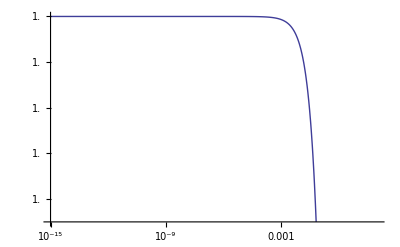

```mathematica
LogLogPlot[(Ye-negenfun[etae]/nb)/Ye,{etae,10^(-15),100}]
```

```mathematica
solsTrad[[1,2]]
```

1.1994×10^8

```mathematica
sols=getetae[Yefun,Ye,myprec];
```

```mathematica
npairs
```

Indeterminate

```mathematica
solsTrad={T->10^9}
```

{T→1000000000}

```mathematica
{neplus,neminus,negen,peplus,peminus,petot,ueplus,ueminus,uetot}=getUPNpairsnoqed
```

After 2 NIntegrates

Before FindRoot

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x$1066918 near {x$1066918} = {4.786721730098975`*^-7}. NIntegrate obtained 4.59675×10^-22 and 9.32426×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x$1066918 near {x$1066918} = {4.786721730098975`*^-7}. NIntegrate obtained 6.23296×10^-23 and 1.25821×10^-25 for the integral and error estimates.

NIntegrate::inumr: The integrand x$1066918^2/1 + ⅇ^-etae$1066919 + 7.242923301787989`*^6 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

NIntegrate::inumr: The integrand x$1066918^2/1 + ⅇ^etae$1066919 + 7.242923301787989`*^6 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x$1066918 near {x$1066918} = {4.786721730098975`*^-7}. NIntegrate obtained 1.69342×10^-22 and 3.42286×10^-25 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

etae0=2.94630375988236585661165415386×10^-14

0.00124614

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

etae0=2.95557840591843734833431423302×10^-14

0.00124614

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

etae0=2.95520960418595306896385972839×10^-14

0.00124614

Finalsoletae

2.94630375988236585661165415386×10^-14

Finalerror

0.00124614

myetae= 2.94630375988236585661165415386×10^-14

After FindRoot

rel error= -0.00124614

{5.42968×10^26,5.42968×10^26,negen$1066918,7.49959×10^19,7.49959×10^19,1.49992×10^20,5.77161×10^20,5.77161×10^20,1.15432×10^21}

```mathematica
myprec=30;
kbT=(kb*T)//.solsTrad;
mecsq=SetPrecision[(me*c^2),myprec];
prefactor=SetPrecision[1/(Pi^2*(hbar*c)^3),myprec];
Ye=SetPrecision[Ye,myprec];
nb=SetPrecision[nb,myprec];
Clear[Ee]
Ee[x_]:=Sqrt[x^2+mecsq^2];
```

```mathematica
fplus[x_,etae_]:=1/(Exp[Ee[x]/(kbT)+etae]+1);
fminus[x_,etae_]:=1/(Exp[Ee[x]/(kbT)-etae]+1);
neplusfun[etae_]:=prefactor*NIntegrate[x^2*fplus[x,etae],{x,0,Infinity}];
neminusfun[etae_]:=prefactor*NIntegrate[x^2*fminus[x,etae],{x,0,Infinity}];
Print["After 2 NIntegrates"];
Yefun[etae_]:=(neminusfun[etae]-neplusfun[etae])/nb;
Print["Before FindRoot"];
(*sols=FindRoot[Yefun[etae]==Ye,{etae,1},WorkingPrecision->myprec];myetae=sols[[1,2]];*)
myetae=getetae[Yefun,Ye,myprec];
Print["myetae= ",myetae];
Print["After FindRoot"];

neplus=neplusfun[myetae];
neminus=neminusfun[myetae];
negen=Yefun[myetae]*nb;
relerror=(Ye-Yefun[myetae])/Ye;
Print["rel error= ",relerror];

(* now get p and u *)
peplus=(prefactor/3)*NIntegrate[x^4/Ee[x]*fplus[x,myetae],{x,0,Infinity}];
peminus=(prefactor/3)*NIntegrate[x^4/Ee[x]*fminus[x,myetae],{x,0,Infinity}];
petot=peplus+peminus;

ueplus=prefactor*NIntegrate[x^2*Ee[x]*fplus[x,myetae],{x,0,Infinity}];
ueminus=prefactor*NIntegrate[x^2*Ee[x]*fminus[x,myetae],{x,0,Infinity}];
uetot=ueplus+ueminus;
```

After 2 NIntegrates

Before FindRoot

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 2.07216×10^-29 and 7.05061×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 2.80437×10^-30 and 9.54197×10^-35 for the integral and error estimates.

NIntegrate::inumr: The integrand x^2/1 + ⅇ^-etaevar + 2.536171871376752`*^7 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

NIntegrate::inumr: The integrand x^2/1 + ⅇ^etaevar + 2.536171871376752`*^7 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 7.62306×10^-30 and 2.59378×10^-34 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

etae0=6.55672342330113859002387363041×10^-7

9.86629×10^-11

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

etae0=6.55672342294008749074931840095×10^-7

9.86629×10^-11

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

etae0=6.55672341288630458324150550964×10^-7

9.86629×10^-11

Finalsoletae

6.55672342330113859002387363041×10^-7

Finalerror

9.86629×10^-11

myetae= 6.55672342330113859002387363041×10^-7

After FindRoot

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 7.62305×10^-30 and 2.59377×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 7.62306×10^-30 and 2.59378×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 7.62305×10^-30 and 2.59377×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 7.62306×10^-30 and 2.59378×10^-34 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.1455080417555052`*^-7}. NIntegrate obtained 7.62305×10^-30 and 2.59377×10^-34 for the integral and error estimates.

rel error= -9.86629×10^-11

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.786721730098975`*^-7}. NIntegrate obtained 9.01719×10^-37 and 6.89921×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.786721730098975`*^-7}. NIntegrate obtained 9.0172×10^-37 and 6.89922×10^-39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.4890464281602789`*^-6}. NIntegrate obtained 6.7178×10^-36 and 1.51985×10^-40 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.4890464281602789`*^-6}. NIntegrate obtained 6.71781×10^-36 and 1.51985×10^-40 for the integral and error estimates.

```mathematica
NIntegrate[T^a,{T,0,1}]
```

NIntegrate::inumr: The integrand T^a has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

```mathematica
NIntegrate[T^a,{T,0,1}]//.{a->1}
```

NIntegrate::inumr: The integrand T^a has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

0.5

```mathematica
Integrate[T^a,{T,0,1}]
```

```mathematica
If[Re[a]>-1,1/(1+a),Integrate[T^a,{T,0,1},Assumptions->Re[a]≤-1]]//.{a->1}
```

1/2

```mathematica
getUPNpairsnoqed
```

After 2 NIntegrates

Before FindRoot

After FindRoot

NIntegrate::inumr: The integrand x$178589^2/1 + ⅇ^-1 + 7.242923301787989`*^15 √Plus[« 2 »]/T has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

NIntegrate::inumr: The integrand x$178589^2/1 + ⅇ^1 + 7.242923301787989`*^15 √Plus[« 2 »]/T has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::nlnum: The function value {2.`30. (0.5`30. - 1.55996241144596966248940432359918958519789578`30.*^-14 (3.20634237944059494487395908315048224327219544064`30.*^48 NIntegrate[Times[« 2 »], {« 3 »}] - 3.20634237944059494487395908315048224327219544064`30.*^48 NIntegrate[Times[« 2 »], {« 3 »}]))} is not a list of numbers with dimensions {1} at {etaevar} = {9.999999999999999999999999999999999999999999`30.*^-16}.

General::stop: Further output of FindRoot will be suppressed during this calculation.

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

Finalsoletae

1

Finalerror

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,1],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,1],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

Finalsoletae

1

Finalerror

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,1],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,1],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

Finalsoletae

1

Finalerror

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,1],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,1],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

Finalsoletae

1

Finalerror

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,1],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,1],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

Finalsoletae

1

Finalerror

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,1],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,1],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

Finalsoletae

1

Finalerror

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,1],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,1],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

Finalsoletae

1

Finalerror

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,1],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,1],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

Finalsoletae

1

Finalerror

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,1],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,1],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

Finalsoletae

1

Finalerror

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,1],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,1],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

Finalsoletae

1

Finalerror

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,1],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,1],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

Finalsoletae

1

Finalerror

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,1],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,1],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

Finalsoletae

1

Finalerror

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,1],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,1],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

Finalsoletae

1

Finalerror

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,1],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,1],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

Finalsoletae

1

Finalerror

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,1],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,1],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fminus$178589[x$178589,0],{x$178589,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x$178589^2 fplus$178589[x$178589,0],{x$178589,0,∞}])]

Finalsoletae

1

Finalerror

$Aborted

```mathematica
var=If[Head[asdf]==Symbol,1,0]
var=If[Head[asdf]==Reals,1,0]
```

1

If[Symbol==Reals,1,0]

```mathematica
NumberQ[asdf]
NumberQ[1324]
NumberQ[1324.13]
```

False

True

True

```mathematica
var=If[!NumberQ[T],1,0]
var=If[!NumberQ[1324],1,0]
```

1

0

```mathematica
Clear[Ee,fplus,fminus,neplus,neminus,negen,x,etae,kbT];
myprec=30;
kbT=(kb*T);
mecsq=SetPrecision[(me*c^2),myprec];
prefactor=SetPrecision[1/(Pi^2*(hbar*c)^3),myprec];
Ye=SetPrecision[Ye,myprec];
nb=SetPrecision[nb,myprec];
Ee[x_]:=Sqrt[x^2+mecsq^2];
fplus[x_,etae_]:=1/(Exp[Ee[x]/(kbT)+etae]+1);
fminus[x_,etae_]:=1/(Exp[Ee[x]/(kbT)-etae]+1);
neplusfun[etae_]:=prefactor*NIntegrate[x^2*fplus[x,etae],{x,0,Infinity}];
neminusfun[etae_]:=prefactor*NIntegrate[x^2*fminus[x,etae],{x,0,Infinity}];
Print["After 2 NIntegrates"];
Yefun[etae_]:=(neminusfun[etae]-neplusfun[etae])/nb;
Print["Before FindRoot"];
(*sols=FindRoot[Yefun[etae]==Ye,{etae,1},WorkingPrecision->myprec];myetae=sols[[1,2]];*)
```

After 2 NIntegrates

Before FindRoot

```mathematica
NIntegrate[T^x,{T,0,1}]
```

NIntegrate::inumr: The integrand T^x has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

NIntegrate[T^x,{T,0,1}]

```mathematica
NIntegrate[T^x,{T,0,1}]//.{x->1}
```

NIntegrate::inumr: The integrand T^x has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

0.5

```mathematica
NIntegrate[T^x,{T,0,1}]
```

```mathematica
InputForm[x+2]
```

2 + x

```mathematica
2 + x//.{x->1}
```

3

```mathematica
getetae[Yefun,Ye,T,myprec]//.{T->10^9}
```

Need T as number

Hold[getetae[Yefun,0.5,1000000000,30]]

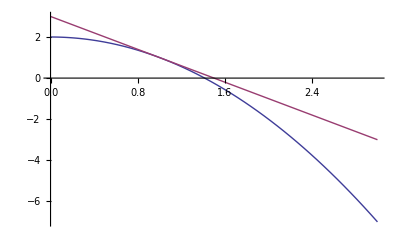

```mathematica
Plot[{2-y^2,3-2*y},{y,0,3}]
```

```mathematica
N[17/12.]
```

1.41667

```mathematica
N[Sqrt[2]]
```

1.41421

```mathematica
godfunc[x_]:=x^2
devilfunc:=x^3
doit[thefunc_,devilfunc_,x_]:=Module[
{foo,y},
y=godfunc[x];
y2=devilfunc;
z=10*y;
z2=10*y2;
{z,z2}
];
doit2[devilfunc_]:=Module[
{foo,y},
y2=devilfunc;
z2=10*y2;
z2
];
```

```mathematica
doit2[devilfunc]
```

10 x^3

```mathematica
godfunc[2]
```

4

```mathematica
doit[godfunc,devilfunc,x]
doit[godfunc,devilfunc,2]
```

{10 x^2,10 x^3}

{40,10 x^3}

```mathematica
getetae[Yefun,0.5,1000000000,30]
```

NIntegrate::inumr: The integrand x^2/1 + ⅇ^-1 + 7.242923301787989`*^15 √« 1 »/T has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

NIntegrate::inumr: The integrand x^2/1 + ⅇ^1 + 7.242923301787989`*^15 √« 1 »/T has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (2.` (0.5`  - 1.55996241144596966248940432359918958519789578`30.*^-14 (3.20634237944059494487395908315048224327219544064`30.*^48 NIntegrate[Times[« 2 »], {« 3 »}] - 3.20634237944059494487395908315048224327219544064`30.*^48 NIntegrate[Times[« 2 »], {« 3 »}])) == 0) is less than WorkingPrecision (30.).

FindRoot::nlnum: The function value {2.`30. (0.5`30. - 1.55996241144596966248940432359918958519789578`30.*^-14 (3.20634237944059494487395908315048224327219544064`30.*^48 NIntegrate[Times[« 2 »], {« 3 »}] - 3.20634237944059494487395908315048224327219544064`30.*^48 NIntegrate[Times[« 2 »], {« 3 »}]))} is not a list of numbers with dimensions {1} at {etaevar} = {9.999999999999999999999999999999999999999999`30.*^-16}.

FindRoot::precw: The precision of the argument function (2.` (0.5`  - 1.55996241144596966248940432359918958519789578`30.*^-14 (3.20634237944059494487395908315048224327219544064`30.*^48 NIntegrate[Times[« 2 »], {« 3 »}] - 3.20634237944059494487395908315048224327219544064`30.*^48 NIntegrate[Times[« 2 »], {« 3 »}])) == 0) is less than WorkingPrecision (30.).

FindRoot::nlnum: The function value {2.`30. (0.5`30. - 1.55996241144596966248940432359918958519789578`30.*^-14 (3.20634237944059494487395908315048224327219544064`30.*^48 NIntegrate[Times[« 2 »], {« 3 »}] - 3.20634237944059494487395908315048224327219544064`30.*^48 NIntegrate[Times[« 2 »], {« 3 »}]))} is not a list of numbers with dimensions {1} at {etaevar} = {9.999999999999999999999999999999999999999999`30.*^-16}.

FindRoot::precw: The precision of the argument function (2.` (0.5`  - 1.55996241144596966248940432359918958519789578`30.*^-14 (3.20634237944059494487395908315048224327219544064`30.*^48 NIntegrate[Times[« 2 »], {« 3 »}] - 3.20634237944059494487395908315048224327219544064`30.*^48 NIntegrate[Times[« 2 »], {« 3 »}])) == 0) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot will be suppressed during this calculation.

FindRoot::nlnum: The function value {2.`30. (0.5`30. - 1.55996241144596966248940432359918958519789578`30.*^-14 (3.20634237944059494487395908315048224327219544064`30.*^48 NIntegrate[Times[« 2 »], {« 3 »}] - 3.20634237944059494487395908315048224327219544064`30.*^48 NIntegrate[Times[« 2 »], {« 3 »}]))} is not a list of numbers with dimensions {1} at {etaevar} = {9.999999999999999999999999999999999999999999`30.*^-16}.

General::stop: Further output of FindRoot will be suppressed during this calculation.

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x^2 fminus[x,0],{x,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x^2 fplus[x,0],{x,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x^2 fminus[x,0],{x,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x^2 fplus[x,0],{x,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x^2 fminus[x,0],{x,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x^2 fplus[x,0],{x,0,∞}])]

Finalsoletae

1

Finalerror

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x^2 fminus[x,1],{x,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x^2 fplus[x,1],{x,0,∞}])]

1

```mathematica
ReleaseHold[getetae[Yefun,Ye,T,myprec]//.{T->10^9}]
```

Need T as number

NIntegrate::inumr: The integrand x^2/1 + ⅇ^-1 + 7.242923301787989`*^15 √« 1 »/T has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

NIntegrate::inumr: The integrand x^2/1 + ⅇ^1 + 7.242923301787989`*^15 √« 1 »/T has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::nlnum: The function value {2.`30. (0.5`30. - 1.55996241144596966248940432359918958519789578`30.*^-14 (3.20634237944059494487395908315048224327219544064`30.*^48 NIntegrate[Times[« 2 »], {« 3 »}] - 3.20634237944059494487395908315048224327219544064`30.*^48 NIntegrate[Times[« 2 »], {« 3 »}]))} is not a list of numbers with dimensions {1} at {etaevar} = {9.999999999999999999999999999999999999999999`30.*^-16}.

General::stop: Further output of FindRoot will be suppressed during this calculation.

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x^2 fminus[x,0],{x,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x^2 fplus[x,0],{x,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x^2 fminus[x,0],{x,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x^2 fplus[x,0],{x,0,∞}])]

etae0=0

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x^2 fminus[x,0],{x,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x^2 fplus[x,0],{x,0,∞}])]

Finalsoletae

1

Finalerror

2. Abs[0.5-1.5599624114459696624894043236×10^-14 (3.20634237944059494487395908315×10^48 NIntegrate[x^2 fminus[x,1],{x,0,∞}]-3.20634237944059494487395908315×10^48 NIntegrate[x^2 fplus[x,1],{x,0,∞}])]

1

```mathematica
getUPNpairs
```

After 2 NIntegrates

Before FindRoot

After FindRoot

```mathematica
Ppairs0noqed[10^8]
Ppairs0qed[10^8]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x$794877 near {x$794877} = {1.1455080417555052`*^-7}. NIntegrate obtained 3.12092×10^-66 and 7.28546×10^-70 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x$794877 near {x$794877} = {1.1455080417555052`*^-7}. NIntegrate obtained 4.14051×10^-43 and 9.66558×10^-47 for the integral and error estimates.

442529.

0.0000930941+7.7936×10^-41 T^4

```mathematica
tempib1[x0_]=Module[{x},Simplify[Integrate[BesselK[5/3,x],{x,x0,Infinity}],{x0>0}]]; (* go ahead and compute this *)
```

```mathematica
tempib1[2.0]
```

0.150818

```mathematica
Ppairs0[10^8]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x$794648 near {x$794648} = {1.1455080417555052`*^-7}. NIntegrate obtained 3.12092×10^-66 and 7.28546×10^-70 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x$794648 near {x$794648} = {1.1455080417555052`*^-7}. NIntegrate obtained 4.14051×10^-43 and 9.66558×10^-47 for the integral and error estimates.

442529.

```mathematica
e2[T_]:=If[1=!=Underflow[],1,0];
```

SetDelayed::write: Tag Power in ⅇ^-Min[10000.`, 0.000016809992004827158` T][T_] is Protected.

```mathematica
e2[10^8]
```

8.93970415121×10^-731

```mathematica
Ppairs0[10^8]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x$749765 near {x$749765} = {1.1455080417555052`*^-7}. NIntegrate obtained 7.46028×10^-47 and 3.51845×10^-50 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x$749765 near {x$749765} = {1.1455080417555052`*^-7}. NIntegrate obtained 1.00964×10^-47 and 4.7617×10^-51 for the integral and error estimates.

NIntegrate::inumr: The integrand x$749765^2/1 + ⅇ^-etaevar + 7.242923301787989`*^7 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

NIntegrate::inumr: The integrand x$749765^2/1 + ⅇ^etaevar + 7.242923301787989`*^7 √Plus[« 2 »] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x$749765 near {x$749765} = {1.1455080417555052`*^-7}. NIntegrate obtained 2.74448×10^-47 and 1.29436×10^-50 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

etae0=1.0000000000000252435489670724×10^-15

1.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

etae0=0.100000000000000000000000000028

1.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

etae0=26.6210740942413079352917123514

1.11022×10^-15

Finalsoletae

26.6210740942413079352917123514

Finalerror

1.11022×10^-15

1.06878079314686498162465302772×10^48 NIntegrate[(x$749765^4 fminus$749765[x$749765,myetae$749765[100000000]])/Ee$749765[x$749765],{x$749765,0,∞}]+1.06878079314686498162465302772×10^48 NIntegrate[(x$749765^4 fplus$749765[x$749765,myetae$749765[100000000]])/Ee$749765[x$749765],{x$749765,0,∞}]